```mathematica
Roots[x(x-1)==0,x]
```

x==1||x==0

```mathematica
Roots[Exp[I*x](x)==0,x]
```

Roots::neq: ⅇ^(ⅈ x) x is expected to be a polynomial in the variable x.

Roots[ⅇ^(ⅈ x) x==0,x]

```mathematica
Exp[0]
```

1

```mathematica
Exp[I*0]
```

1

```mathematica
Exp[I*5]
```

ⅇ^(5 ⅈ)

```mathematica
N[ⅇ^(5 ⅈ)]
```

0.283662-0.958924 ⅈ

```mathematica
Roots[-wn^2+2g*wn*I+w^2==0,wn]
```

wn==ⅈ g-√(-g^2+w^2)||wn==ⅈ g+√(-g^2+w^2)

```mathematica
C1*Exp[I*g+Sqrt[g&2+]]
```

```mathematica
Solve[-wn^2+2g*wn*I+w^2==0,wn]//Simplify
```

{{wn→ⅈ g-√(-g^2+w^2)},{wn→ⅈ g+√(-g^2+w^2)}}

```mathematica
C1=1
C2=1
k=1
g=1
```

1

1

1

«1 more identical outputs»

```mathematica
t=5
```

5

```mathematica
1
```

1

```mathematica
Exp[-I*t]//Abs
```

1

```mathematica
A*Exp[-I*w*T]+B*Exp[I*w*T]//ExpToTrig//Simplify
```

(A+B) Cos[T w]-ⅈ (A-B) Sin[T w]

```mathematica
Refine[A*Exp[-I*w*T]+B*Exp[I*w*T],Element[A,Reals]]
```

A ⅇ^(-ⅈ T w)+B ⅇ^(ⅈ T w)

```mathematica
Cos[T w]-ⅈ Re[Sin[T w]]//Re
```

Re[Cos[T w]]

```mathematica
Re[x+I*Re[y]]
```

Re[x]

```mathematica
ExpToTrig[Re[ⅇ^(-5 ⅈ w)]]
```

Im[Sin[5 w]]+Re[Cos[5 w]]

```mathematica
Re[Exp[I*w*t]]//ExpToTrig
```

-Im[Sin[5 w]]+Re[Cos[5 w]]

```mathematica
Refine[
Re[Exp[I*Ω*T]],
{Element[T,Reals],Element[Ω,Reals]}]
```

Re[ⅇ^(ⅈ T Ω)]

```mathematica
Exp[I*Ω*T]//ExpToTrig
```

Cos[T Ω]+ⅈ Sin[T Ω]

```mathematica
Refine[
Re[Cos[T Ω]+ⅈ Sin[T Ω]],
{Element[T,Reals],Element[Ω,Reals]}]
```

Cos[T Ω]

```mathematica
(A1+I*B1)Exp[-I*Ω*T]//ExpToTrig//Expand
```

A1 Cos[T Ω]+ⅈ B1 Cos[T Ω]-ⅈ A1 Sin[T Ω]+B1 Sin[T Ω]

```mathematica
(A1+I*B1)Exp[-I*Ω*T]+(A2+I*B2)Exp[+I*Ω*T]//ExpToTrig//Expand
```

A1 Cos[T Ω]+A2 Cos[T Ω]+ⅈ B1 Cos[T Ω]+ⅈ B2 Cos[T Ω]-ⅈ A1 Sin[T Ω]+ⅈ A2 Sin[T Ω]+B1 Sin[T Ω]-B2 Sin[T Ω]

```mathematica
A*Exp[I*x]+B*Exp[-I*x]//ExpToTrig
```

A Cos[x]+B Cos[x]+ⅈ A Sin[x]-ⅈ B Sin[x]

```mathematica
Refine[Re[A Cos[x]+B Cos[x]+ⅈ A Sin[x]-ⅈ B Sin[x]],{Element[A,Reals],Element[B,Reals],Element[x,Reals]}]
```

A Cos[x]+B Cos[x]

```mathematica
FullSimplify[A Cos[x]+B Cos[x]+ⅈ A Sin[x]-ⅈ B Sin[x]]
```

(A+B) Cos[x]+ⅈ (A-B) Sin[x]

```mathematica
Exp[-g*t] (C1 Exp[ⅈ t √(k^2-g^2)]+C2 Exp[-ⅈ t √(k^2-g^2)])//Re
```

2 Re[ⅇ^-t]

```mathematica
(A1 Exp[ⅈ t √(κ^2-γ^2)]+B1 Exp[-ⅈ t √(κ^2-γ^2)])
```

B1 ⅇ^(-ⅈ t √(-γ^2+κ^2))+A1 ⅇ^(ⅈ t √(-γ^2+κ^2))

```mathematica
Simplify[B1 ⅇ^(-ⅈ t √(-γ^2+κ^2))+A1 ⅇ^(ⅈ t √(-γ^2+κ^2))]
```

```mathematica
ⅇ^(-ⅈ t √(-γ^2+κ^2)) (B1+A1 ⅇ^(2 ⅈ t √(-γ^2+κ^2)))//ExpToTrig
```

```mathematica
(Cos[t √(-γ^2+κ^2)]-ⅈ Sin[t √(-γ^2+κ^2)]) (B1+A1 Cos[2 t √(-γ^2+κ^2)]+ⅈ A1 Sin[2 t √(-γ^2+κ^2)])//Simplify
```

```mathematica
(A1+B1) Cos[t √(-γ^2+κ^2)]+ⅈ (A1-B1) Sin[t √(-γ^2+κ^2)]
```

(A1+B1) Cos[t √(-γ^2+κ^2)]+ⅈ (A1-B1) Sin[t √(-γ^2+κ^2)]

```mathematica
A1 Cos[t √(-γ^2+κ^2)]+B1 Cos[t √(-γ^2+κ^2)]+ⅈ A1 Sin[t √(-γ^2+κ^2)]-ⅈ B1 Sin[t √(-γ^2+κ^2)]
```

A1 Cos[t √(-γ^2+κ^2)]+B1 Cos[t √(-γ^2+κ^2)]+ⅈ A1 Sin[t √(-γ^2+κ^2)]-ⅈ B1 Sin[t √(-γ^2+κ^2)]

```mathematica
Manipulate[Plot[2 Cos[t √(-γ^2+κ^2)] (Cosh[t γ]-Sinh[t γ]),{t,-8,8}],{γ,-8,8},{κ,-2,2}]
```

```mathematica
ExpToTrig[Real[ⅇ^(-t γ) (ⅇ^(-ⅈ t √(-γ^2+κ^2))+ⅇ^(ⅈ t √(-γ^2+κ^2)))]]
```

Real[ⅇ^(-t γ) (ⅇ^(-ⅈ t √(-γ^2+κ^2))+ⅇ^(ⅈ t √(-γ^2+κ^2)))]

```mathematica
Simplify[Real[ⅇ^(-t γ) (ⅇ^(-ⅈ t √(-γ^2+κ^2))+ⅇ^(ⅈ t √(-γ^2+κ^2)))]]
```

Real[ⅇ^(-t γ-ⅈ t √(-γ^2+κ^2)) (1+ⅇ^(2 ⅈ t √(-γ^2+κ^2)))]

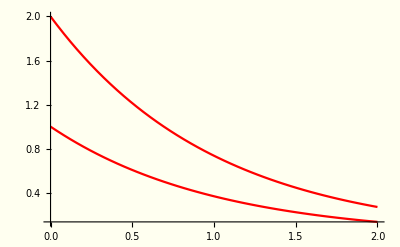

```mathematica
Plot[{Exp[-g*t],Exp[-g*t] (C1 Exp[ⅈ t √(k^2-g^2)]+C2 Exp[-ⅈ t √(k^2-g^2)])},{t,0,2},PlotTheme->"Minimal",Background->RGBColor[1.,1.,0.94117],PlotStyle->{Red},PlotRange->Full]
```

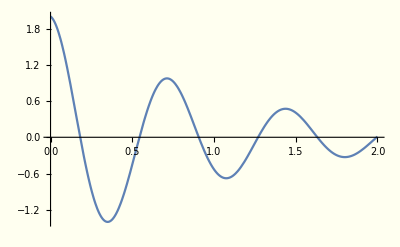

```mathematica
Show[%84,Background->RGBColor[1.,1.,0.94117]]
```

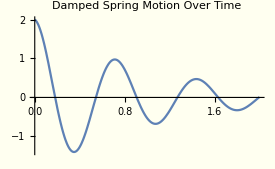

```mathematica
Show[%90,PlotLabel->HoldForm[Damped Spring Motion Over Time],Style->"Red"]
```

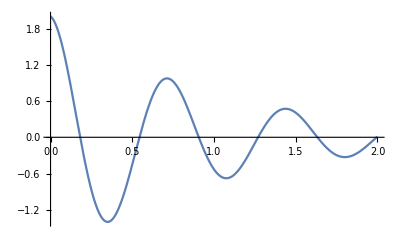

```mathematica
Show[%67,Background->RGBColor[255,255,240]]
```

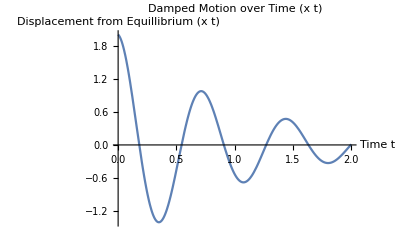

```mathematica
Show[%64,AxesLabel->{HoldForm[Time t],HoldForm[Displacement from Equillibrium (x t)]},PlotLabel->HoldForm[Damped Motion over Time (x t)],LabelStyle->{GrayLevel[0]}]
```

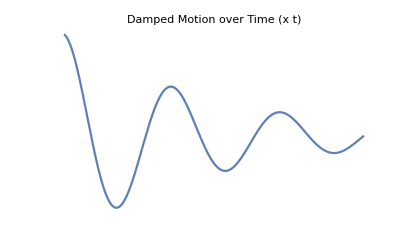

```mathematica
Show[%65,Axes->False]
```